Task 1.1c

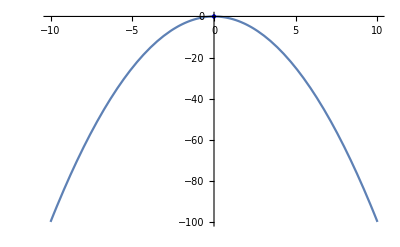

```mathematica
h=0;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = x/. roots;
Plot[h+x(r-x),{x,-10,10}, Epilog->{Blue,PointSize@Large,Point[{{Part[roots,1],0},{Part[roots,2],0}}]}]
```

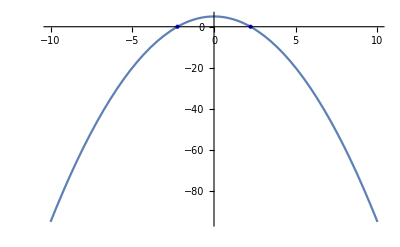

```mathematica
h=5;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = x/. roots;
Plot[h+x(r-x),{x,-10,10}, Epilog->{Blue,PointSize@Large,Point[{{Part[roots,1],0},{Part[roots,2],0}}]}]
```

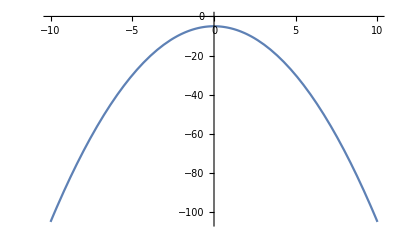

```mathematica
h=-5;
r=0;
roots=Solve[h+x(r-x)==0,x];
roots = rootsForX=x/. roots;
Plot[h+x(r-x),{x,-10,10}]
```

```mathematica
ContourPlot3D[h+x(r-x)==0,{x,-10,10},{h,-10,10},{r,-10,10}]
```

-Graphics3D-

```mathematica
f[x_]:=h+x(r-x)
f'[x]
```

```mathematica
prim = r-2 x;
xstar = x/.Solve[prim==0,x];

hc = h/.Solve[f[xstar]==0,h]
```

{-r^2/4}

```mathematica
Task 1.1d
```

1.2 Subcritical pitchfork

```mathematica
f[x_] = r*x+4x^3-9x^5;
roots= x/.Solve[f'[x]==0,x];
p1= Plot[{roots},{r,-2,2},PlotStyle->{{Black,Dashing[Tiny]},{Black,Dashing[Tiny]},{Black,Line},{Black,Line}}];
p2 = Plot[{0},{r,-2,0},PlotStyle->{Black}];
p3 = Plot[{0},{r,0,2},PlotStyle->{Black,Dashing[Tiny]}];
Show[p1,p2,p3]
```

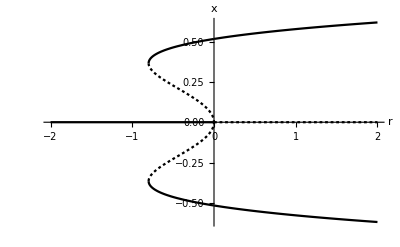

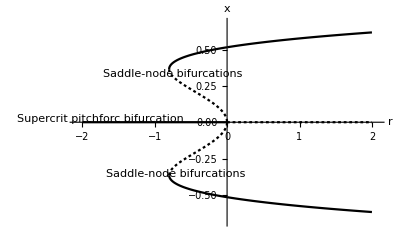

```mathematica
Show[%2586,AxesLabel->{HoldForm[r],HoldForm[x]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
Manipulate[Plot[r*x+4x^3-9x^5,{x,-1,1}],{r,-1,1}]
```